# Time Constant Calculator from Simulation Data

## Setup (automatically initialized when this notebook is opened)

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {}.

```mathematica
OrganizeWFData[fileName_]:=Module[{axesLabel,d,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
Return[{axesLabel,d}];
](* OrganizeWFData Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]]
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts

File Name: LPFWaveform_Im_tau_0.01_Immax214f.txt

## Information Processing (Run-time)

### Process Waveform data from input file

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBounds ={0.5,1.5};
data=.;
AbsoluteTiming[data=OrganizeWFData[fileName]];
axesLabel=data⟦1⟧;
d=data⟦2⟧;
selectedData=Select[d,#⟦1⟧>timeBounds⟦1⟧&];
selectedData=Select[selectedData,#⟦1⟧<=timeBounds⟦2⟧&];
Isat=Max[Transpose[selectedData]⟦2⟧];
offset=Last[Transpose[selectedData]⟦2⟧];
offsetMin=Min[Transpose[selectedData]⟦2⟧]-10^-17;
```

2.14039×10^-13

#### Plot Data

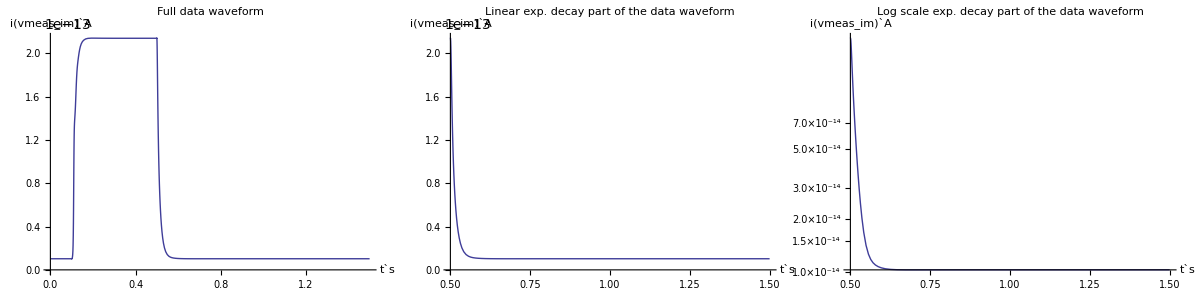
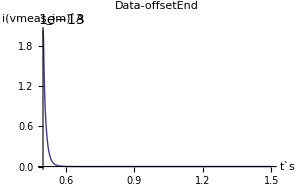
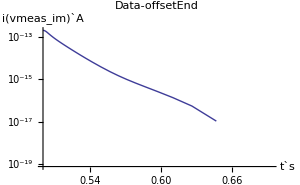
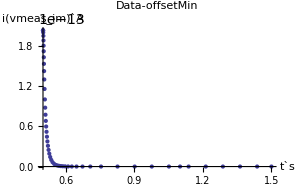
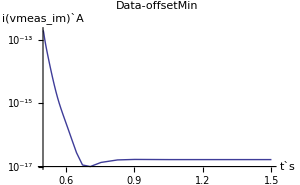
Data Waveforms
-Graphics-
Data without offset Waveforms
Linear Plot | Log Plot
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
imgSize=300;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold]],
ListLinePlot[selectedData,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Linear exp. decay part of the data waveform",Bold]],
ListLogPlot[selectedData,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize, PlotLabel->Style["Log scale exp. decay part of the data waveform",Bold]]}
}]},
{Text[Style["Data without offset Waveforms",Bold,18]]},
{Grid[{
{Text[Style["Linear Plot",Bold,14]],Text[Style["Log Plot",Bold,14]]},
{ListLinePlot[selectedData-offset,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Data-offsetEnd",Bold]],
ListLogPlot[selectedData-offset,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize,PlotLabel->Style["Data-offsetEnd",Bold]]},
{ListPlot[selectedData-offsetMin,AxesLabel->axesLabel,ImageSize->imgSize,PlotLabel->Style["Data-offsetMin",Bold]],
ListLogPlot[selectedData-offsetMin,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize,PlotLabel->Style["Data-offsetMin",Bold]]}
}]}
}]
```

### Manipulate Data

#### Calculate τ using exponential fit including offset

```mathematica
Manipulate[
dataBoundsExp={lowerBoundExp,upperBoundExp};
selectedDataExp=Select[selectedData,#⟦2⟧>0&];
xValsExp=Transpose[selectedDataExp]⟦1⟧;
selDataExp=Select[selectedDataExp,#⟦1⟧>dataBoundsExp⟦1⟧&];
selDataExp=Select[selDataExp,#⟦1⟧<dataBoundsExp⟦2⟧&];
(*fooLine=Fit[selDataExp,{1,Exp[-t]},t]*)
model=(a Exp[-t/τexp])+o;
fooCurveParams=FindFit[selDataExp,model,{a,τexp,o},t,MaxIterations->2000];
fooCurve=Function[{t},Evaluate[model/.fooCurveParams]];
Grid[{
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[a/.fooCurveParams,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[o/.fooCurveParams,Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τexp/.fooCurveParams,Italic]}]},
{Show[ListPlot[selDataExp,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],
ListLogPlot[selDataExp,AxesLabel->axesLabel,ImageSize->imgSize],
Plot[fooCurve[t],{t,0,upperBoundExp}]
]}
}],
{{lowerBoundExp,0.501,"Lower Bound"},0.5,1.0,.001,Appearance->{"Labeled","Open"}},
{{upperBoundExp,xValsExp⟦Floor[Length[xValsExp]/2]⟧,"Upper Bound"},xValsExp,Appearance->{"Labeled","Open"}}
]
```

## Appendix

#### Calculate τ using linear fit of log of exponential decay (old method of doing this)

```mathematica
Manipulate[
dataBounds={lowerBound,upperBound};
selData=Select[selectedData-offsetMin,#⟦2⟧>0&];
xVals=Transpose[selData]⟦1⟧;
logSelectedData=Transpose[{selData⟦;;,1⟧,Log[selData⟦;;,2⟧]}];
logSelData=Select[logSelectedData,#⟦1⟧>dataBounds⟦1⟧&];
logSelData=Select[logSelData,#⟦1⟧<dataBounds⟦2⟧&];
fooLine=Fit[logSelData,{1,t},t];
barLine=FindFit[logSelData,m t+b,{m,b},t];
τ=-1/m/.barLine;
Grid[{
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[Isat,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMin,Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τ,Italic]}]},
{Show[ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],
ListLogPlot[selData,AxesLabel->axesLabel,ImageSize->imgSize],
Plot[fooLine,{t,0,0.7}]
]}
}],
{{lowerBound,0.501,"Lower Bound"},0.5,1.0,.001,Appearance->{"Labeled","Open"}},
{{upperBound,xVals⟦Floor[Length[xVals]/2]⟧,"Upper Bound"},xVals,Appearance->{"Labeled","Open"}}
]
```